```mathematica
<<arnoldi2x2.m
```

```mathematica
σ2
```

{1/2 (α+β+ξ11+ξ22-√((-α-β-ξ11-ξ22)^2-4 (α β+β ξ11-ξ12 ξ21+α ξ22+ξ11 ξ22))),1/2 (α+β+ξ11+ξ22+√((-α-β-ξ11-ξ22)^2-4 (α β+β ξ11-ξ12 ξ21+α ξ22+ξ11 ξ22)))}

```mathematica
Expand[(-α-β-ξ11-ξ22)^2-4 (α β+β ξ11-ξ12 ξ21+α ξ22+ξ11 ξ22)]
```

α^2-2 α β+β^2+2 α ξ11-2 β ξ11+ξ11^2+4 ξ12 ξ21-2 α ξ22+2 β ξ22-2 ξ11 ξ22+ξ22^2

```mathematica
s[α_,β_,ξ11_,ξ12_,ξ21_,ξ22_]={1/2 (α+β+ξ11+ξ22-√(α^2-2 α β+β^2+2 α ξ11-2 β ξ11+4 ξ12 ξ21-2 α ξ22+2 β ξ22-2 ξ11 ξ22)),1/2 (α+β+ξ11+ξ22+√(α^2-2 α β+β^2+2 α ξ11-2 β ξ11+4 ξ12 ξ21-2 α ξ22+2 β ξ22-2 ξ11 ξ22))};
```

```mathematica
bias2[α_,β_,ξ11_,ξ12_,ξ21_,ξ22_]=FullSimplify[s[α,β,ξ11,ξ12,ξ21,ξ22]-s[α,β,0,0,0,0]]
```

{1/2 (√((α-β)^2)+ξ11+ξ22-√((α-β) (α-β+2 ξ11)+4 ξ12 ξ21-2 (α-β+ξ11) ξ22)),1/2 (-√((α-β)^2)+ξ11+ξ22+√((α-β) (α-β+2 ξ11)+4 ξ12 ξ21-2 (α-β+ξ11) ξ22))}

```mathematica
ExpectedValue[bias2[α,β,ξ,ξ,ξ,ξ],NormalDistribution[0,1],ξ,Assumptions->α>β]
```

{1/2 (α-β-2 HypergeometricU[-1/2,0,1/4 (α-β)^2]),1/2 (-α+β+2 HypergeometricU[-1/2,0,1/4 (α-β)^2])}

```mathematica
s2s[α_,β_,ξ11_,ξ12_,ξ21_,ξ22_]=σ2
```

{1/2 (α+β+ξ11+ξ22-√((-α-β-ξ11-ξ22)^2-4 (α β+β ξ11-ξ12 ξ21+α ξ22+ξ11 ξ22))),1/2 (α+β+ξ11+ξ22+√((-α-β-ξ11-ξ22)^2-4 (α β+β ξ11-ξ12 ξ21+α ξ22+ξ11 ξ22)))}

```mathematica
realbias[α_,β_,ξ11_,ξ12_,ξ21_,ξ22_]=Simplify[s2s[α,β,ξ11,ξ12,ξ21,ξ22]-s2s[α,β,0,0,0,0],Assumptions->α>β]
```

{1/2 (α-β+ξ11+ξ22-√(α^2+β^2-2 β ξ11+ξ11^2+4 ξ12 ξ21+2 β ξ22-2 ξ11 ξ22+ξ22^2-2 α (β-ξ11+ξ22))),1/2 (-α+β+ξ11+ξ22+√(α^2+β^2-2 β ξ11+ξ11^2+4 ξ12 ξ21+2 β ξ22-2 ξ11 ξ22+ξ22^2-2 α (β-ξ11+ξ22)))}

```mathematica
Limit[Limit[Limit[Limit[realbias[α,β,ξ11,ξ12,ξ21,ξ22],ξ11->0],ξ12->0],ξ21->0],ξ22->0]
```

{1/2 (α-√((α-β)^2)-β),1/2 (-α+√((α-β)^2)+β)}

```mathematica
a[α_,β_,Σ_]=ExpectedValue[realbias[α,β,ξ,ξ,ξ,ξ],NormalDistribution[0,Σ],ξ,Assumptions->α>β]
```

{1/2 (α-β-2 √2 Σ HypergeometricU[-1/2,0,(α-β)^2/(8 Σ^2)]),1/2 (-α+β+2 √2 Σ HypergeometricU[-1/2,0,(α-β)^2/(8 Σ^2)])}

```mathematica
Manipulate[LogLogPlot[{a[α,β,Σ][[2]]},{Σ,1 10^-5,xmax},
PlotStyle->{{Red,Thick}, {Blue}},FrameLabel->{"Standard Deviation","Eigenvalue Bias"},
Frame->{{True, False},{True, False}},LabelStyle->Directive[FontFamily->"Helvetica", FontSize->24], RotateLabel->True,
ImageSize->{934, Automatic}],
{{α,10},0,100},{{β,9},0,α},{{xmax,10},0.001,1000}]
```

```mathematica
,
```

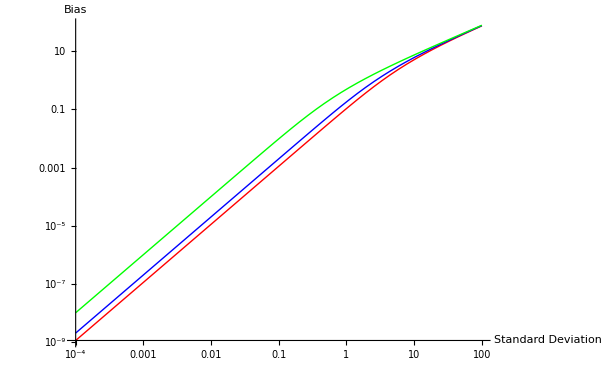

```mathematica
LogLogPlot[{a[10,1,Σ][[2]],a[10,5,Σ][[2]],a[10,9,Σ][[2]]},{Σ,0.0001,100}, PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},AxesLabel->{"Standard Deviation","Bias"}]
```

```mathematica
Manipulate[LogLogPlot[{a[α,β,Σ][[2]]},{Σ,1 10^-5,xmax},PlotStyle->{{Red,Thick}},AxesLabel->{"Standard Deviation","Bias"}],{{α,5},0,10},{β,0,10},{{xmax,1},0.001,100}]
```

```mathematica
b[α_,β_,Σ_]=ExpectedValue[realbias[α,β,ξ,ξ,ξ,ξ],UniformDistribution[{-Σ,Σ}],ξ,Assumptions->α>β]
```

{(4 α Σ-4 β Σ-2 Σ √(α^2-2 α β+β^2+4 Σ^2)-α^2 ArcSinh[(2 Σ)/(α-β)]+2 α β ArcSinh[(2 Σ)/(α-β)]-β^2 ArcSinh[(2 Σ)/(α-β)])/(8 Σ),(-4 α Σ+4 β Σ+2 Σ √(α^2-2 α β+β^2+4 Σ^2)+α^2 ArcSinh[(2 Σ)/(α-β)]-2 α β ArcSinh[(2 Σ)/(α-β)]+β^2 ArcSinh[(2 Σ)/(α-β)])/(8 Σ)}

```mathematica
Manipulate[Plot[{b[α,β,Σ][[2]]},{Σ,0,xmax},PlotStyle->{{Red,Thick}},AxesLabel->{"Variance","Bias"}],{{α,5},0,10},{β,0,10},{{xmax,1},0.001,100}]
```

```mathematica
Manipulate[{N[a[α,β]]//MatrixForm,N[b[α,β]]//MatrixForm},{{α,5},β,10},{{β,0},0,10}]
```

```mathematica
ExpectedValue[realbias[α,β,ξ11,ξ12,ξ21,ξ22],NormalDistribution[0,1],ξ12]
```

$Aborted

```mathematica
p[x_,Σ_]=PDF[NormalDistribution[0,Σ],x]
```

(ⅇ^(-x^2/(2 Σ^2)))/(√(2 π) Σ)

```mathematica
u[x_,min_,max_]=PDF[UniformDistribution[{min,max}],x]
```

Piecewise[{{1/(max-min), min≤x≤max}}]

```mathematica
x={1,2,3,4,5,6}
```

{1,2,3,4,5,6}

```mathematica
Apply[realbias,x]
```

{1/2 (8-4 √6),1/2 (10+4 √6)}

```mathematica
Table[realbias[10,1,RandomReal[NormalDistribution[0,1]],RandomReal[NormalDistribution[0,1]],RandomReal[NormalDistribution[0,1]],RandomReal[NormalDistribution[0,1]]][[1]],{i,1,1000000}];
```

```mathematica
nums = Table[{10, 9, RandomReal[NormalDistribution[0,1.]],RandomReal[NormalDistribution[0,1.]],RandomReal[NormalDistribution[0,1.]],RandomReal[NormalDistribution[0,1.]]},{i,1,1000000}];
```

```mathematica
Timing[Table[{RandomReal[NormalDistribution[0.,1.]]},{i,1,1000000}];]
```

{4.05556,Null}

```mathematica
Timing[moreNums = Map[Apply[realbias, #]&,nums];]
```

{40.5016,Null}

```mathematica
Mean[moreNums]
```

{-0.24094-0.18457 ⅈ,0.241963+0.18457 ⅈ}

```mathematica
StandardDeviation[moreNums]
```

{1.01414,1.01415}

```mathematica
moreNums[[1]]
```

{-0.490516,0.164092}

```mathematica
Table[1,{i,1,1000000}];
```

```mathematica
NIntegrate[p[ξ11,1]p[ξ12,1]p[ξ21,1]p[ξ22,1]realbias[10,1,ξ11,ξ12,ξ21,ξ22][[1]],{ξ11,-10,10},{ξ12,-10,10},{ξ21,-10,10},{ξ22,-10,10},WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001652058425641265699 - 3.997357898623082426×10^-6\ ⅈ and 9.3922905466257153951×10^-6 for the integral and error estimates.

0.001652058425641265699-3.997357898623082426×10^-6 ⅈ

```mathematica
Abs[1+ⅈ]
```

√2

```mathematica
NIntegrate[p[ξ11,1]p[ξ12,1]p[ξ21,1]p[ξ22,1]Abs[realbias[10,1,ξ11,ξ12,ξ21,ξ22][[1]]],{ξ11,-10,10},{ξ12,-10,10},{ξ21,-10,10},{ξ22,-10,10},WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.80345100923585581161 and 0.000043172014009560237493 for the integral and error estimates.

0.80345100923585581161

```mathematica
Plot3D[p[ξ1,1]p[ξ2,1]Abs[realbias[10,1,ξ1,ξ1,ξ2,ξ2][[1]]],{ξ1,-10,10},{ξ2,-10,10}, PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[{(*p[ξ1,1]p[ξ2,1]*)realbias[10,1,ξ1,ξ1,ξ2,ξ2][[1]],0},{ξ1,-10,10},{ξ2,-10,10}, PlotRange->All,PlotPoints->100]
```

-Graphics3D-

```mathematica
Plot3D[{p[ξ1,1]p[ξ2,1]realbias[10,1,ξ1,ξ1,ξ2,ξ2][[1]]},{ξ1,-10,10},{ξ2,-10,10}, PlotRange->All,PlotPoints->100]
```

-Graphics3D-

```mathematica
Plot3D[{p[ξ1,.1]p[ξ2,.1]realbias[10,1,ξ1,ξ1,ξ2,ξ2][[1]]},{ξ1,-10,10},{ξ2,-10,10}, PlotRange->All,PlotPoints->100]
```

-Graphics3D-

```mathematica
NIntegrate[p[ξ1,1]p[ξ2,1]Re[realbias[10,1,ξ1,ξ1,ξ2,ξ2][[1]]],{ξ1,-5,5},{ξ2,-5,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00602682 and 1.02937×10^-8 for the integral and error estimates.

0.00602682

```mathematica
NIntegrate[p[ξ11,1]p[ξ12,1]p[ξ21,1]p[ξ22,1]realbias[10,1,ξ11,ξ12,ξ21,ξ22][[2]],{ξ11,-10,10},{ξ12,-10,10},{ξ21,-10,10},{ξ22,-10,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00165204 + 3.99658×10^-6\ ⅈ and 9.39446×10^-6 for the integral and error estimates.

-0.00165204+3.99658×10^-6 ⅈ

```mathematica
NIntegrate[p[ξ11,1]p[ξ12,1]p[ξ21,1]p[ξ22,1]realbias[10,9,ξ11,ξ12,ξ21,ξ22][[1]],{ξ11,-10,10},{ξ12,-10,10},{ξ21,-10,10},{ξ22,-10,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.241136 - 0.184138\ ⅈ and 0.00313372 for the integral and error estimates.

-0.241136-0.184138 ⅈ

```mathematica
NIntegrate[p[ξ11,1]p[ξ12,1]p[ξ21,1]p[ξ22,1]realbias[10,9,ξ11,ξ12,ξ21,ξ22][[2]],{ξ11,-10,10},{ξ12,-10,10},{ξ21,-10,10},{ξ22,-10,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.241155  + 0.184142\ ⅈ and 0.00314758 for the integral and error estimates.

0.241155+0.184142 ⅈ

```mathematica
NIntegrate[u[ξ11,-0.5,0.5]u[ξ12,-0.5,0.5]u[ξ21,-0.5,0.5]u[ξ22,-0.5,0.5]realbias[10,1,ξ11,ξ12,ξ21,ξ22][[1]],{ξ11,-10,10},{ξ12,-10,10},{ξ21,-10,10},{ξ22,-10,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.64525×10^-6 and 8.99443×10^-9 for the integral and error estimates.

9.64525×10^-6

```mathematica
NIntegrate[u[ξ11,-0.5,0.5]u[ξ12,-0.5,0.5]u[ξ21,-0.5,0.5]u[ξ22,-0.5,0.5]realbias[10,1,ξ11,ξ12,ξ21,ξ22][[2]],{ξ11,-10,10},{ξ12,-10,10},{ξ21,-10,10},{ξ22,-10,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.64525×10^-6 and 9.24507×10^-9 for the integral and error estimates.

-9.64525×10^-6

```mathematica
NIntegrate[u[ξ11,-0.5,0.5]u[ξ12,-0.5,0.5]u[ξ21,-0.5,0.5]u[ξ22,-0.5,0.5]realbias[10,9,ξ11,ξ12,ξ21,ξ22][[1]],{ξ11,-10,10},{ξ12,-10,10},{ξ21,-10,10},{ξ22,-10,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00684419  - 0.0123826\ ⅈ and 0.007151 for the integral and error estimates.

0.00684419-0.0123826 ⅈ

```mathematica
NIntegrate[u[ξ11,-0.5,0.5]u[ξ12,-0.5,0.5]u[ξ21,-0.5,0.5]u[ξ22,-0.5,0.5]realbias[10,9,ξ11,ξ12,ξ21,ξ22][[2]],{ξ11,-10,10},{ξ12,-10,10},{ξ21,-10,10},{ξ22,-10,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00718004 + 0.0121513\ ⅈ and 0.00737715 for the integral and error estimates.

-0.00718004+0.0121513 ⅈ